## LineEdgeIntersection-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 20:47:51
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

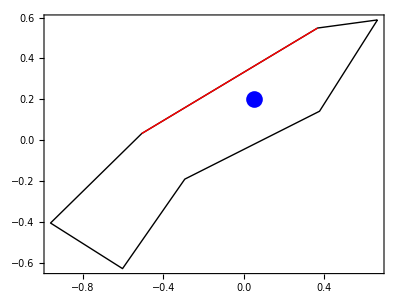

```mathematica
polygon={{0.6656821861024209,0.5885139068629628},{0.3674265409089722,0.548792012192189},{-0.5083022778120968,0.03200749861905844},{-0.9625187848327785,-0.40634552703524995},{-0.603944818863048,-0.6296344493677282},{-0.2938861906733466,-0.19134629851828722},{0.3771323695082593,0.14124017268253336}};
edge={{0.3674265409089722,0.548792012192189},{-0.5083022778120968,0.03200749861905844}}; 
point1={0.05,0.2}; 
Show[Boundary[polygon],
Graphics[{Blue, PointSize[.03], Point[point1], Red, Thick, Line[edge]}], 
 Frame-> True]
```

```mathematica
LineEdgeIntersection[edge, point1, {1,.5}]
```

$Failed

```mathematica
int=LineEdgeIntersection[edge, point1, {-1,1}]
```

{-0.0515474,0.301547}

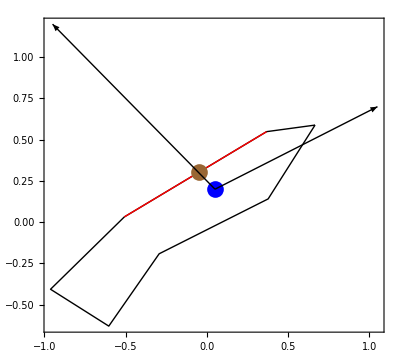

```mathematica
Show[Boundary[polygon],
Graphics[{Blue, PointSize[.03], Point[point1], Red, Thick, Line[edge],Brown, Point[int], Thin, Black, Arrow[{point1, point1+{-1,1}}], 
Arrow[{point1, point1+{1,.5}}]}], 
 Frame-> True]
```